```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

```mathematica
Ebert, Faustov, Galkin, arXiv:1007.1369 [hep-ph]
```

## Init

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<MyPackages`ChDim`
```

```mathematica
ClearScalarProducts[];
ScalarProduct[p1, p1]=MBc^2; ScalarProduct[p2, p2]=Mcc^2; ScalarProduct[q,q]=q2;
ScalarProduct[p1,p2]=Calc[(SP[p1]+SP[p2]-SP[q])/2];
ScalarProduct[p1, q]=Calc[(SP[p1]+SP[q]-SP[p2])/2];
ScalarProduct[p2,q]=Calc[(SP[p1]-SP[p2]-SP[q])/2];
Calc[SP[#]&/@{p2+q, p1-q, p1-p2}]
```

{MBc^2,Mcc^2,q2}

```mathematica
SetOptions[ChDim, Dimensions->{
GF->-2,
a1->0, beta->0, Vbc->0, Vuq->0,
mu->0,a->0, b->0,
rhoL[_]->0, rhoT[_]->0,
fPlus[_]->0, fMinus[_]->0,
hA[_]->0, hV1[_]->0, hV2[_]->0, hV3[_]->0,
tV[_]->0, tA1[_]->0, tA2[_]->0, tA3[_]->0,
fP->1, mP->1, fV->1, mV->1,
p1->1, p2->1,q->1, MBc->1, Mcc->1,
q2->2}];
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

## Amplitudes

```mathematica
ffList={}
```

{}

```mathematica
Clear[amplitude];
amplitude::usage = "amplitude[out, |\"A\"|\"V\"] is the amplitude for Bc -> out decay, see relations (2)-(4) from the article";
amplitude[out_, "V+A"]:=amplitude[out,"V"]+amplitude[out,"A"];
```

```mathematica
Join[{1},{2}]
```

{1,2}

```mathematica
(* (19) *)
out = "chi_c0";
amplitude[out, "V"]=0;
amplitude[out, "A"]=fPlus[q2]FV[p1+p2,mu]+fMinus[q2]FV[p1-p2,mu];
ffList = DeleteDuplicates[Join[ffList,{fPlus, fMinus}]];
```

```mathematica
ChDim[amplitude[out, "A"]]
```

0.00871224 $M

```mathematica
(* (20) *)
out = "chi_c1";
amplitude[out,"V"]=(MBc+Mcc)hV1[q2]MT[mu,a]+(hV2[q2]FV[p1,mu]+hV3[q2]FV[p2,mu])FV[q,a]/MBc;
amplitude[out, "A"]=(2I hA[q2])/(MBc+Mcc)LeviCivita[mu,a][p1,p2];
ffList = DeleteDuplicates[Join[ffList,{hV1, hV2, hV3, hA}]];
```

```mathematica
ChDim[amplitude[out, "V"]//Calc]
```

0.016545 $M

```mathematica
(* (22) *)
out = "chi_c2";
amplitude[out,"V"]=(2I tV[q2])/(MBc+Mcc)LeviCivita[mu,a][p1,p2] FV[p1,b]/MBc;
amplitude[out, "A"]=(MBc+Mcc)tA1[q2]*MT[mu,b] FV[p1,a]/MBc+
(tA2[q2]FV[p1,mu]+tA3[q2]FV[p2,mu])(FV[p1,a]FV[p1,b])/MBc^2;
ffList = DeleteDuplicates[Join[ffList,{tV, tA1, tA2, tA3}]];
```

```mathematica
ChDim[amplitude[out, "A"]//Calc]
```

0.00435219 $M

```mathematica
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,chiList},{t,{"A","V"}}]
```

{chi_c0,A}	-0.0917684 $M

{chi_c0,V}	0

{chi_c1,A}	(0.+0.327048 ⅈ) $M

{chi_c1,V}	0.397535 $M

{chi_c2,A}	0.000937346 $M

{chi_c2,V}	(0.+0.00967142 ⅈ) $M

```mathematica
amplitude[out_,"V+A"]:=amplitude[out, "V"]+amplitude[out,"A"];
Do[Print[{out,t}, "\t",ChDim[FCI[amplitude[out, t]]]],{out,chiList},{t,{"A","V", "V+A"}}]
```

{chi_c0,A}	0.121688 $M

{chi_c0,V}	0

{chi_c0,V+A}	-0.0132479 $M

{chi_c1,A}	(0.+0.000152981 ⅈ) $M

{chi_c1,V}	0.0937249 $M

{chi_c1,V+A}	(0.534357+0.253097 ⅈ) $M

{chi_c2,A}	0.00696729 $M

{chi_c2,V}	(0.+0.015664 ⅈ) $M

{chi_c2,V+A}	(0.62283+0.0530688 ⅈ) $M

## Widths

```mathematica
J[a_, b_]:=PolarizationSum[a, b, p2];
J2[{a_,b_},{ca_, cb_}]:=(J[a, ca]*J[b,cb]+J[a,cb]*J[b,ca])/2-J[a,b]J[ca,cb]/3
```

```mathematica
{Calc[J2[{a,a},{ca, cb}]],
Calc[J2[{a,b},{ca, ca}]],
Calc[J2[{ca,cb},{ca, cb}]]}
```

{0,0,5}

```mathematica
Clear[outPol];
outPol["L", "P"]=(-I fP FV[p1-p2,mu]);
outPol["L","V"]=mV*fV;
outPol["L","W"]=1;
```

```mathematica
Clear[outPol2];
outPol2["L","P"]=1;
outPol2["L","V"]=PolarizationSum[mu, ci[mu], q];
outPol2["L","W"]=(FV[q, mu]FV[q,ci[mu]]-SP[q]*MT[mu, ci[mu]])*rhoT[q2]+FV[q,mu]FV[q,ci[mu]]rhoL[q2];
outPol2["H","chi_c0"]=1;
outPol2["H","chi_c1"]=PolarizationSum[a,ci[a],p2];
outPol2["H", "chi_c2"]=J2[{a,b},{ci[a],ci[b]}];
```

```mathematica
Clear[gamma];
PrintTemporary[Dynamic[{out, outL}]];
Do[
matr = GF/(√2)Vbc Vuq a1 amplitude[out, "V+A"]*outPol["L",outL];
matr = Simplify[Contract[matr]];
cmatr = ComplexConjugate[matr]/.{LorentzIndex[m_]:>LorentzIndex[ci[m]]};
matr2 = matr*cmatr*outPol2["L", outL]*outPol2["H", out];
matr2 = Simplify[Contract[matr2]];
gamma[out, outL] = Simplify[1/(2MBc)beta/(8Pi)matr2];
,{out, chiList},{outL,{"P", "V", "W"}}];
```

```mathematica
Do[
Print[{out, outL},"\t",ChDim[gamma[out, outL]]];
,{out, chiList},{outL,{"P","V","W"}}]
```

{chi_c0,P}	1.30483×10^-8 $M

{chi_c0,V}	1.49113×10^-10 $M

{chi_c0,W}	0.0000675944/($M)

{chi_c1,P}	7.64541×10^-6 $M

{chi_c1,V}	6.91266×10^-6 $M

{chi_c1,W}	(7.5817×10^-8)/($M)

{chi_c2,P}	3.0336×10^-9 $M

{chi_c2,V}	0.000097523 $M

{chi_c2,W}	0.0000797642/($M)

## Form Factors

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
tab$fPlus = Import["../literatute/Ebert_FFs/chi0_fPlus.csv"];
tab$fMinus = Import["../literatute/Ebert_FFs/chi0_minusFminus.csv"];
tab$fMinus⟦All,2⟧=-tab$fMinus⟦All,2⟧;
```

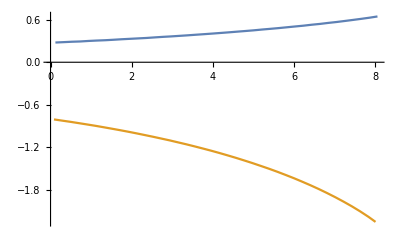

```mathematica
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

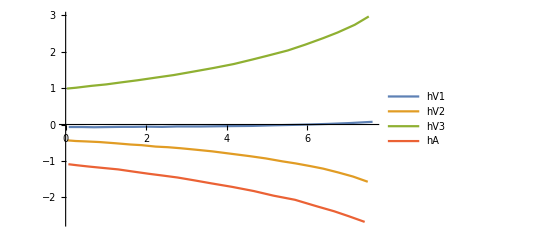

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_1P.json"];
tab$hV1 = extractFF[chic1,1]["data"];
tab$hV2 = extractFF[chic1,2, -1]["data"];
tab$hV3 = extractFF[chic1,3]["data"];
tab$hA = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

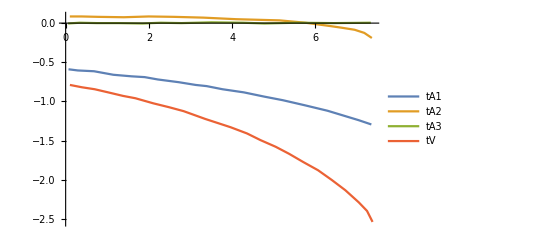

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_1P.json"];
tab$tA3 = extractFF[chic2, 1]["data"];
tab$tA2 = extractFF[chic2, 2]["data"];
tab$tA1 = extractFF[chic2, 3, -1]["data"];
tab$tV = extractFF[chic2, 4,-1]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
?FindFit
```

```mathematica
?Select
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

## Numbers

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
getMcc[out_]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
```

```mathematica
ffRule = (ToExpression[#]->Interpolation[ToExpression["tab$"<>ToString[#]]])&/@ffList;
```

```mathematica
GeV=1; MeV=10^-3 GeV;
```

```mathematica
Clear[Ngamma];
Ngamma[out_, outL_]:=Module[{
$Mcc=getMcc[out],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->1.14
}//.{MBc -> 6274.47MeV, mPi->140MeV, mV->770MeV, Mcc->$Mcc, q2->$q2}/.ffFitRule]
```

```mathematica
10^15/1.14^2 Ngamma["chi_c0", "P"]
```

0.227085

```mathematica
10^15/1.14^2 Ngamma["chi_c1", "P"]
```

0.0128168

```mathematica
10^15/1.14^2 Ngamma["chi_c2", "P"]
```

0.392902

```mathematica
distEE["chi_c0"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic0_1P.json"], 1]["data"];
distEE["chi_c1"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic1_1P.json"], 1]["data"];
distEE["chi_c2"] = extractFF[Import["../literatute/Ebert_FFs/fig4_chic2_1P.json"], 1]["data"];
```

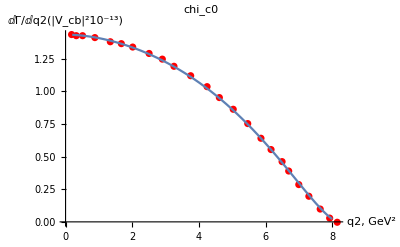

```mathematica
out = "chi_c0";
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```

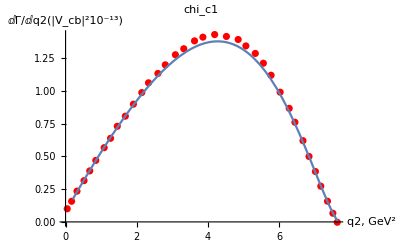

```mathematica
out = "chi_c1";
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```

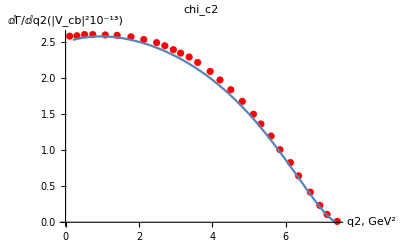

```mathematica
out = "chi_c2";
Show[
ListPlot[distEE[out], PlotStyle->Red],
Plot[0.8 10^13/(40.8*10^-3)^2 Ngamma[out,"W"]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}, {q2, 0.2,8}]
, AxesLabel->{"q2, GeV^2", "ⅆΓ/ⅆq2(|V_cb|^210^-13)"}, PlotLabel->out]
```